```mathematica
List/@1->2
```

1->2

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}},{{{0,0},{0,0}}},3,"CausalGraphStructure",AspectRatio->1/2]
```

```mathematica
GraphData["Cayley"]
```

```mathematica
Labeled[Framed[#, Graphics[Text["h"]]]]&/@Range[100]
```

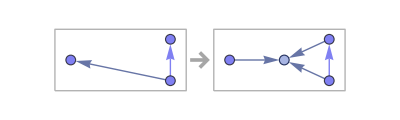

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,y},{x,w},{y,w},{z,w}}]]
```

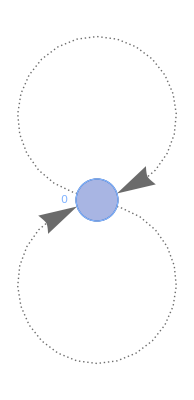
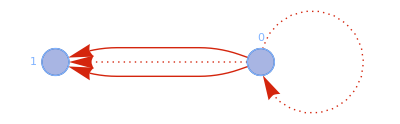
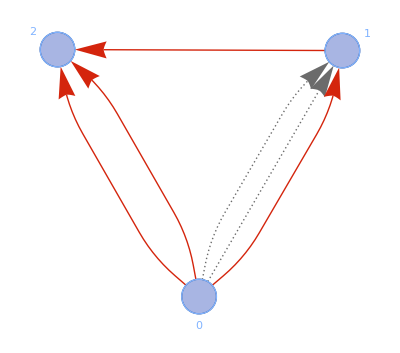
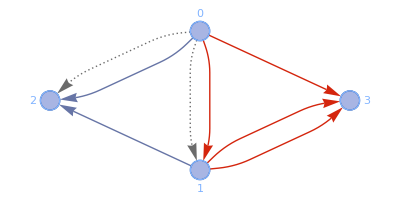
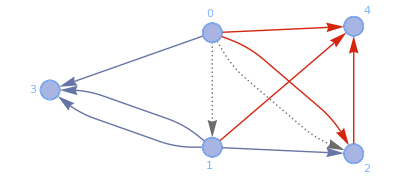
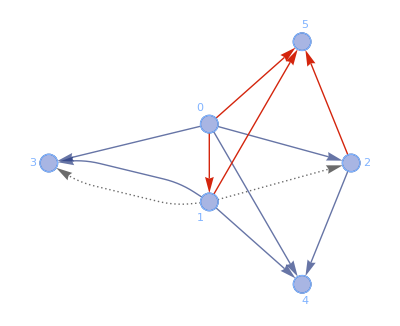
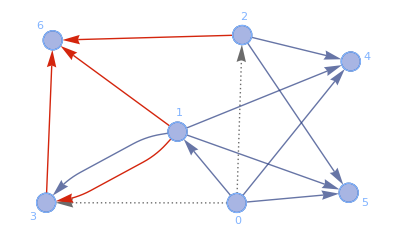
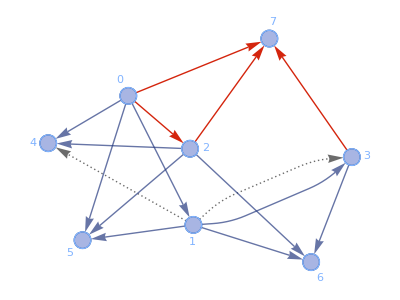

```mathematica
With[{eo=ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},4]},TakeList[eo["EventsStatesPlotsList",ImageSize->Tiny,VertexLabels->Automatic],eo["GenerationEventsCountList","IncludeBoundaryEvents"->"Initial"]]]
```